```mathematica
Be=0.37h 100 c;
ωe=634 100 c 2 π;
c = 2.99792458*^8;
h = 6.62607004*^-34;
ℏ = h/(2π);
kb = 1.38064852*^-23;
T=300;
A=135*100 c;
vibMaxBoltz[v_,T_]:=(Exp[-ℏ ωe/(2kb T)](1-Exp[-ℏ ωe/(kb T)])^-1)^-1 Exp[-ℏ (ωe(v+1/2))/(kb T)]
MaxBoltz[v_,J_,T_]:=vibMaxBoltz[v,T]((2J+1)Exp[-(Be (J(J+1)-(3/2)^2))/(kb T)])/Sum[(2k+1)Exp[-(Be( k(k+1)-(3/2)^2))/(kb T)],{k,3/2,300+3/2}]
```

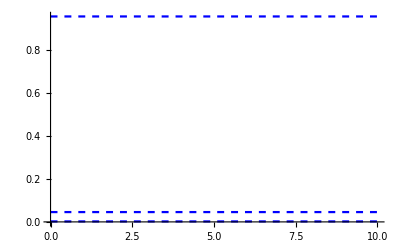

```mathematica
Plot[{Sum[MaxBoltz[0,k,T],{k,0,100}],Sum[MaxBoltz[2,k,T],{k,0,100}],Sum[MaxBoltz[1,k,T],{k,0,100}]},{t,0,10},PlotStyle->Table[{Blue,Dashed},{i,1,3}]]
```

```mathematica
MBrotPop=Table[MaxBoltz[0,J,T],{J,0,100}];
```

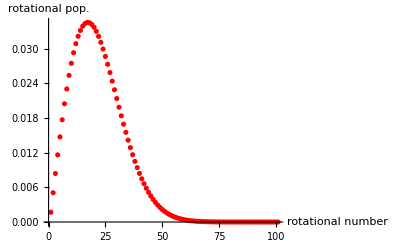

```mathematica
ListPlot[{MBrotPop},AxesLabel->{"rotational number","rotational pop."},PlotStyle->{Red,Dashed},PlotRange->All]
```

```mathematica
MaxBoltz[0,1.5,300]*2/(Exp[-h A/(kb T)]+2)
```

0.00533943

```mathematica
MaxBoltz[0,2.5,300]*2/(Exp[-h A/(kb T)]+2)
```

0.0079384

```mathematica
MaxBoltz[0,3.5,300]*2/(Exp[-h A/(kb T)]+2)
```

0.0104539

```mathematica
MaxBoltz[0,4.5,300]*2/(Exp[-h A/(kb T)]+2)
```

0.0128603

```mathematica
Elec=1/(Exp[-h A/(kb T)]+1)
```

0.656436

```mathematica
kb T
```

4.14195×10^-21

```mathematica
ℏ (2π*A)/(kb T)
```

0.64745

```mathematica
A
```

4.0472×10^12